```mathematica
With[{img=ColorConvert[ExampleData[{"TestImage","Lena"}],"Grayscale"]},ImageMultiply[img,Graphics[{White,Disk[]},Background->None]]]
```

-Graphics-

```mathematica
img=ColorConvert[ExampleData[{"TestImage","Lena"}],"Grayscale"];
ImageTransformation[img,If[Norm[#-0.5]<0.5,#,{-0.1,-0.1}]&]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
img =ImageData[ ColorConvert[Import["mouse.jpg"],"Grayscale"]];
```

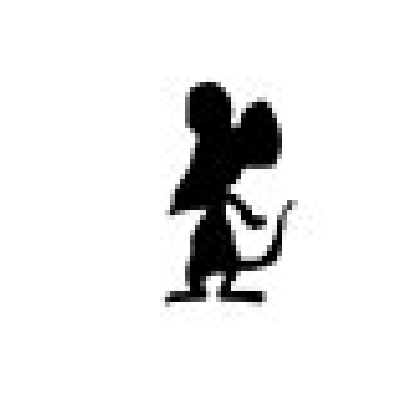

```mathematica
ArrayPlot[img]
```

```mathematica
ImageData[ColorConvert[ExampleData[{"TestImage","Lena"}],"Grayscale"]]
```

{{0.635294,0.635294,0.635294,0.631373,0.635294,0.615686,0.639216,0.631373,497,0.643137,0.658824,0.666667,0.670588,0.666667,0.607843,0.501961},510,{1}}
 |  |  |  |

```mathematica
ArrayPlot[%35,ColorFunction->GrayLevel,ColorFunctionScaling->False]
```

-Graphics-